```mathematica
data={{1935.221075,11.2},{1916.371519,10.8},{1897.521963,9.8},{1872.389222,9.2},{1840.973295,8.6},{1979.203372,13.8},{2042.035225,13.4},{2073.451151,13},{2123.716634,11.2},{2142.56619,10.4},{2173.982116,9.4}};
```

```mathematica
fit= NonlinearModelFit[data,B/(Sqrt[(R^2-w^2)^2+(2*β*w)^2]),{B,β,R},w]
```

FittedModel[…]

```mathematica
fit[{"BestFit","ParameterTable"}]
```

{(7.59013×10^6)/(√(72968. w^2+(4.14687×10^6-w^2)^2)), | Estimate | Standard Error | t-Statistic | P-Value
B | 7.59013×10^6 | 277323. | 27.3693 | 3.42372×10^-9
β | -135.063 | 6.64568 | -20.3234 | 3.59123×10^-8
R | 2036.39 | 3.49156 | 583.231 | 8.36478×10^-20}

```mathematica
plotfit=Plot[fit[w],{w,0,3000},PlotLegends->{"Curva A(ω)"},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Thick},PlotRange->{{1830,2200},{8.2,14}},Frame->True,FrameLabel->{Style["ω / rad s⁻.b9",Bold,16],Style[" A(ω) / mV",16,Bold]},Epilog->{Text[Style["2Δω",Black],{2025,10.2}]}];
```

```mathematica
Maximize[fit[w],w]
```

{13.8286,{w→-2027.41}}

```mathematica
FindRoot[fit[w]==13.828648307291006/Sqrt[2],{w,1900}]
```

{271.322→1887.2}

```mathematica
FindRoot[fit[w]==13.828648307291006/Sqrt[2],{w,2200}]
```

{271.322→2158.53}

```mathematica
2δω=2158.5317329581967-1887.1988768106512
```

Set::write: Tag Times in 2 δω is Protected.

271.333

```mathematica
anch=Plot[13.828648307291006/Sqrt[2],{w,1887.1988768106512,2158.5317329581967},BaseStyle->{FontFamily->"Calibri",FontSize->14},PlotStyle->{Blend[{Blue,White}],Dashed},PlotRange->{{1887.1988768106512,2158.5317329581967},{5,15}},PlotLegends->{"A(ω)/Sqrt[2] / mV"},Frame->True,FrameLabel->{Style["θ / rad",Bold,16],Style["V(θ) / J",16,Bold]}];
```

```mathematica
Needs["ErrorBarPlots`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
dataerr1=ErrorListPlot[{{{1935.221075,11.2},ErrorBar[6.3,0.1]},{{1916.371519,10.8},ErrorBar[6.3,0.1]},{{1897.521963,9.8},ErrorBar[6.3,0.1]},{{1872.389222,9.2},ErrorBar[6.3,0.1]},{{1840.973295,8.6},ErrorBar[6.3,0.1]},{{1979.203372,13.8},ErrorBar[6.3,0.1]},{{2042.035225,13.4},ErrorBar[6.3,0.1]},{{2073.451151,13},ErrorBar[6.3,0.1]},{{2123.716634,11.2},ErrorBar[6.3,0.1]},{{2142.56619,10.4},ErrorBar[6.3,0.1]},{{2173.982116,9.4},ErrorBar[6.3,0.1]}},AxesOrigin->{0,0},PlotStyle->{Black,Thickness[0.003]}];
```

```mathematica
plotdata=ListPlot[data ,PlotStyle->{Black,Thickness[0.003]},PlotLegends -> {"Datos experimentales"}];
```

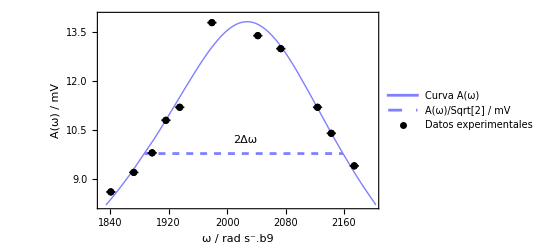

```mathematica
Show[plotfit,anch,plotdata,dataerr1]
```

```mathematica
(*v helio*)
```

```mathematica
Clear[γ,T,M,v]
```

```mathematica
v[γ_,T_,M_]:=Sqrt[(γ*8.3145*T)/M]
```

```mathematica
errHe=Sqrt[(5/3*8.3145)/0.004]/(2*Sqrt[20+273.25])*(0.1)
```

0.171856

```mathematica
erraire=Sqrt[(7/5*8.3145)/0.029]/(2*Sqrt[20+273.25])*(0.1)
```

0.0584971

```mathematica
v[5/3,20+273.15,0.004]
```

1007.76

```mathematica
v[7/5,20+273.15,0.029]
```

343.027

```mathematica
(*delta w*)
```

```mathematica
w=(2*135.0629711855002*Sqrt[2027.4095347046805^2+2*135.0629711855002^2])/(2027.4095347046805)
```

271.322